## Lib + Model Inits

### FCM Lib Import

```mathematica
SetDirectory@NotebookDirectory[]
(*Needs["FCMLib`",FileNameJoin[{NotebookDirectory[],"FCMLib-cur.wl"}]]*)
Needs["FCMLib`",FileNameJoin[{"../lib","FCMLib-cur.wl"}]]
$FCMLibVersion

psotvs=Import["./psot-verts.csv", "CSV"];
psotvs⟦;;,2;;⟧=StringTrim/@psotvs⟦;;,2;;⟧; 

n = Length@psotvs

strongOrLink=$activationThreshold/2-0.001;orLink=strongOrLink-0.05;weakOrLink=$activationThreshold/4;
unsure=orLink;
andLink=$activationThreshold/4;
(* Strong vs Regular indicated by Fig 2.4; Specific to the al Qaeda case *)
(* Extra cross links informed by PD convos or by interpretation of PSOT papers *)

$stdActvnParams = {$activationFxn, $activationBias}
```

/Users/oosoba/Documents/RAND/Coding/fcm-fusion/fcm

Fuzzy Cognitive Map Library ver. 0.0.7+

34

{UnitStep,0.5}

### Setup Non-Threshold activations...

```mathematica
logisticActvn[t_]:=Max[0,LogisticSigmoid[7.5t-3.5]];
SetAttributes[logisticActvn,{Listable,NumericFunction}]

linearActvn[t_]:=Min[Max[0,t],1];
SetAttributes[linearActvn,{Listable,NumericFunction}]


(* LU Activation: *)
{$activationFxn, $activationBias} = {linearActvn, 0};

(* Logistic Activation: *)
(*{$activationFxn, $activationBias} = {logisticActvn, 0};*)

{$activationFxn, $activationBias}

(* To Reset: {$activationFxn, $activationBias}=oldActvnParams; *)
```

{linearActvn,0}

### Model Specifications

#### PSOT v0

```mathematica
psotegsv0={
(* Original Tree structure *)
{1,6,strongOrLink},{2,6,strongOrLink},{3,6,strongOrLink},{4,6,orLink},{5,6,orLink},{30,6,weakOrLink},{31,6,weakOrLink},{32,6,weakOrLink},

{7,10,strongOrLink},{8,10,weakOrLink},{9,10,orLink},{24,10,strongOrLink},

{10,13,strongOrLink},{11,13,strongOrLink},{12,13,weakOrLink},

{14,18,strongOrLink (*unsure*)},{15,18,weakOrLink},{16,18,orLink},{17,18,orLink},

{19,23,strongOrLink (*unsure*)},{20,23,strongOrLink (*unsure*)},{21,23,-strongOrLink},{22,23,-strongOrLink},


(* Loose bits in orig factor tree *)
{25,11,orLink+0.1},(*fudge low fan-in nodes else never triggers*)
{24,7,strongOrLink+0.3},{24,11,strongOrLink},
{23,19,strongOrLink (*unsure*)},{23,20,strongOrLink (*unsure*)},{18,14,strongOrLink (*unsure*)},(*return links for uncertain causation*)


{6,50,andLink},{13,50,andLink},{18,50,andLink},{23,50,andLink} (*,TLD 'and' links*)
(*{50,50,orLink×orLink}, (* weak PSOT self-excitations for temporal correlation(?) *)*)


(*(* see pg 23 in PD+AOM2013 for next set of xlinks *)
{29,13,orLink},{29,21,-orLink},(* s/f links: Effects of successes ,{29,18,orLink} *)
{26,6,-orLink},{26,13,-orLink},(* Effects of Misbehaving grps {26,18,-orLink}, *)

{6,13,weakOrLink},{13,18,weakOrLink},{13,18,weakOrLink},{18,23, weakOrLink},(*rem l->r dep weak links*)
{6,29,weakOrLink} (* eff -> success *)*)
};

psotFCMv0 =FCM[psotvs,psotegsv0,0.7];
```

#### PSOT v1

```mathematica
psotegsv1={
(* Original Tree structure *)
{1,6,strongOrLink},{2,6,strongOrLink},{3,6,strongOrLink},{4,6,orLink},{5,6,orLink},{30,6,weakOrLink},{31,6,weakOrLink},{32,6,weakOrLink},

{7,10,strongOrLink},{8,10,weakOrLink},{9,10,orLink},{24,10,strongOrLink},

{10,13,strongOrLink},{11,13,strongOrLink},{12,13,weakOrLink},

{14,18,strongOrLink (*unsure*)},{15,18,weakOrLink},{16,18,orLink},{17,18,orLink},

{19,23,strongOrLink (*unsure*)},{20,23,strongOrLink (*unsure*)},{21,23,-strongOrLink},{22,23,-strongOrLink},


(* Loose bits in orig factor tree *)
{25,11,orLink+0.1},(*fudge low fan-in nodes else never triggers*)
{24,7,strongOrLink+0.3},{24,11,strongOrLink},
{23,19,strongOrLink (*unsure*)},{23,20,strongOrLink (*unsure*)},{18,14,strongOrLink (*unsure*)},(*return links for uncertain causation*)


{6,50,andLink},{13,50,andLink},{18,50,andLink},{23,50,andLink}, (*TLD 'and' links*)


(* see pg 23 in PD+AOM2013 for next set of xlinks *)
{29,13,orLink},{29,21,-orLink},(*succ links:Effects of successes*)
{6,29,weakOrLink},(*eff->success*)
{33,13,-orLink},{33,21,orLink},(*fail links:Effects of failures*)

{26,6,-strongOrLink},{26,13,-strongOrLink}(* Effects of Misbehaving grps {26,18,-orLink}, *)

(*{6,13,weakOrLink},{13,18,weakOrLink},{18,23, weakOrLink},(*rem l->r dep weak links*)*)
};

psotFCMv1 =FCM[psotvs,psotegsv1,0.7];
```

#### PSOT v2

```mathematica
psotegsv2={
(* Original Tree structure *)
{1,6,strongOrLink},{2,6,strongOrLink},{3,6,strongOrLink},{4,6,orLink},{5,6,orLink},{30,6,weakOrLink},{31,6,weakOrLink},{32,6,weakOrLink},

{7,10,strongOrLink},{8,10,weakOrLink},{9,10,orLink},{24,10,strongOrLink},

{10,13,strongOrLink},{11,13,strongOrLink},{12,13,weakOrLink},

{14,18,strongOrLink (*unsure*)},{15,18,weakOrLink},{16,18,orLink},{17,18,orLink},

{19,23,strongOrLink (*unsure*)},{20,23,strongOrLink (*unsure*)},{21,23,-strongOrLink},{22,23,-strongOrLink},


(* Loose bits in orig factor tree *)
{25,11,orLink+0.1},(*fudge low fan-in nodes else never triggers*)
{24,7,strongOrLink+0.3},{24,11,strongOrLink},
{23,19,strongOrLink (*unsure*)},{23,20,strongOrLink (*unsure*)},{18,14,strongOrLink (*unsure*)},(*return links for uncertain causation*)


{6,50,andLink},{13,50,andLink},{18,50,andLink},{23,50,andLink}, (*TLD 'and' links*)
{50,50,0.1}, (* weak PSOT self-excitations for temporal correlation(?) *)


(* see pg 23 in PD+AOM2013 for next set of xlinks *)
{29,13,orLink},{29,21,-(orLink+0.4)},(*succ links:Effects of successes*)
{6,29,weakOrLink},(*eff->success*)
{33,13,-orLink},{33,21,(orLink+0.4)},(*fail links:Effects of failures*)

{26,6,-strongOrLink},{26,13,-strongOrLink},(* Effects of Misbehaving grps {26,18,-orLink}, *)

{6,13,weakOrLink},{13,18,weakOrLink},{18,23, weakOrLink}(*rem l->r dep weak links*)
};
psotFCMv2 =FCM[psotvs,psotegsv2,0.7];
```

### Model Summaries

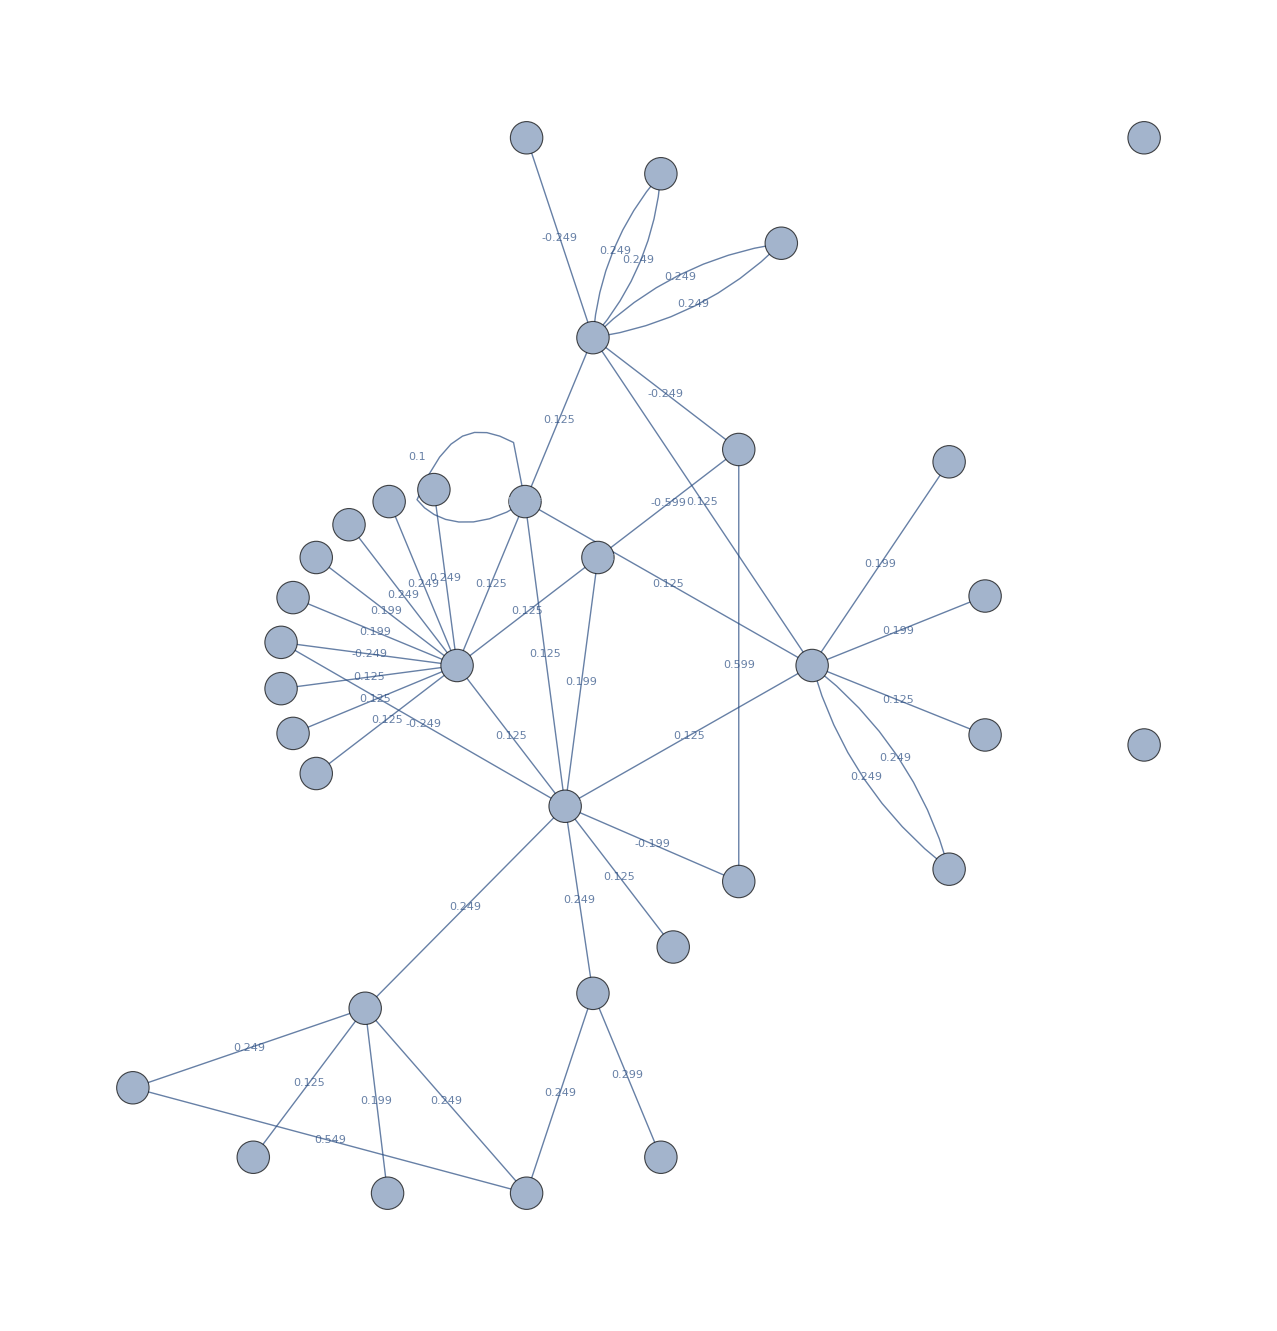

```mathematica
fcms = {psotFCMv0,psotFCMv1,psotFCMv2};

Graph[psotFCMv0,
GraphLayout->"RadialEmbedding",
ImageSize->72×12
]

(*Graph[psotFCMv1,
GraphLayout->"RadialEmbedding",
ImageSize->72×12
]*)

Graph[psotFCMv2,
GraphLayout->"RadialEmbedding",
ImageSize->72×12
]
```

## Continuous Activation Exploration

```mathematica
TableForm[
psotvs,
TableHeadings->{None,Style[#,Bold]&/@{"", "Label", "Full Description"} }
]
```

#### Engineered Masks + Vertex Leverage Analysis

```mathematica
Transpose@{psotvs⟦;;,3⟧,EigenvectorCentrality@psotFCMv0,EigenvectorCentrality@psotFCMv2, (#/Total[#])&@BetweennessCentrality@psotFCMv0,(#/Total[#])&@BetweennessCentrality@psotFCMv2}//TableForm
```

```mathematica
egmask = {1,1,0,1,1,0,0,0,0,0,0,0,1,1,0,1,1,1,1,1,0,0,0,1,0,0,0,0,0,1,0,0,0,0};
eg2mask = {1,1,0,1,1,0,0,0,0,0,0,0,1,1,1,0,1,0,1,1,-1,-1,0,1,0,0,0,0,0,1,0,0,1,0}; (*can use 16-cprop to tip scales for linactvn*)
eg3mask = {1,1,-1,-1,1,0,0,0,0,0,0,0,1,1,1,0,1,0,1,1,-1,-1,0,1,0,0,0,0,0,1,1,0,1,0}; 
Grid[{
{TableForm@Transpose@{Pick[psotvs⟦;;,2⟧,egmask,1],
Pick[psotvs⟦;;,3⟧,egmask,1]}},
{TableForm@Transpose[{Pick[psotvs⟦;;,2⟧,eg2mask,1],Pick[psotvs⟦;;,3⟧,eg2mask,1]}],
Style[TableForm@Transpose[{Pick[psotvs⟦;;,2⟧,eg2mask,-1],Pick[psotvs⟦;;,3⟧,eg2mask,-1]}], Red]},
{TableForm@Transpose[{Pick[psotvs⟦;;,2⟧,eg3mask,1],Pick[psotvs⟦;;,3⟧,eg3mask,1]}],
Style[TableForm@Transpose[{Pick[psotvs⟦;;,2⟧,eg3mask,-1],Pick[psotvs⟦;;,3⟧,eg3mask,-1]}], Red]}
},Frame->All]
```

```mathematica
(* Engineered example that leads diff model behavior *)
Pick[psotvs⟦;;,2⟧,egmask,1]
Pick[psotvs⟦;;,2⟧,egmask,-1]

Pick[psotvs⟦;;,2⟧,eg2mask,1]
Pick[psotvs⟦;;,2⟧,eg2mask,-1]

Pick[psotvs⟦;;,2⟧,eg3mask,1]
Pick[psotvs⟦;;,2⟧,eg3mask,-1]
```

#### Comparisons

```mathematica
Manipulate[
fins=((FCMEvolSeq[#,inp,mask]&)/@fcms);
res=Transpose@{fcms, fins};
Panel[$activationFxn];
Row[{
TableForm[
Transpose[{inp, mask}~Join~Chop[SetAccuracy[fins⟦;;,-1,;;⟧,3],10^-2]],
TableHeadings->{
MapThread[Style[(#1<>#2<>#3), 14]&,{psotvs⟦;;,3⟧,ConstantArray["|", n],psotvs⟦;;,2⟧}],
{"inp", "mask","v0","v1","v2"}
},
TableAlignments->Right, TableSpacing->{2,1.5}
],

TabView[
Table[
(FCMView[Graph[#1, GraphLayout->"RadialEmbedding"], #2, psotvs]&)@@res⟦ev⟧,
{ev,Range@Length@res}
],3
],

GraphicsRow[
MatrixPlot[#, 
ColorRules->{x_/;0≤x≤0.45->LightBlue,x_/;0.45<x≤0.65->Orange,x_/;x≤0.65->White},
ImageSize->Large,
ImageMargins->0,
FrameTicks->{None,Automatic} ,
FrameTicksStyle->Directive[20, Bold]
]&/@(Transpose/@fins),
ImageMargins->0
]

},"|",
ImageSize->72×32
],

{{inp,(*ConstantArray[0,n]*)RandomInteger[{0,1},n]},ControlType->None},
{{mask,(*ConstantArray[0,n]*)eg3mask },ControlType->None},


Dynamic@Panel@Grid[{
{SetterBar[Dynamic[{$activationFxn, $activationBias}],{{linearActvn,0},{logisticActvn,0},{UnitStep,0.5}}], Text[{$activationFxn, $activationBias}]},
Outer[Text[Style[psotvs⟦#,2⟧, 14]]&,Range[n]],
Outer[Checkbox[Dynamic[inp⟦#⟧],{0,1}]&,Range[n]],
Outer[Checkbox[Dynamic[mask⟦#⟧],{0,1,-1}]&,Range[n]]
}, Alignment->Right
]
]
```

```mathematica
(* Old 2-Panel Version *)
Manipulate[
fins=((FCMEvolSeq[#,inp,mask]&)/@fcms);
res=Transpose@{fcms, fins};
Panel[$activationFxn];
Row[{
TableForm[
Transpose[{inp, mask}~Join~Chop[SetAccuracy[fins⟦;;,-1,;;⟧,3],10^-2]],
TableHeadings->{
MapThread[Style[(#1<>#2<>#3), 14]&,{psotvs⟦;;,3⟧,ConstantArray["|", n],psotvs⟦;;,2⟧}],
{"inp", "mask","v0","v1","v2"}
},
TableAlignments->Right, TableSpacing->{2,1.5}
],

TabView[
Table[
(FCMView[Graph[#1, GraphLayout->"RadialEmbedding"], #2, psotvs]&)@@res⟦ev⟧,
{ev,Range@Length@res}
],3
]
},"|",
ImageSize->72×23
],

{{inp,ConstantArray[0,n](*RandomInteger[{0,1},n]*)},ControlType->None},
{{mask,ConstantArray[0,n](*eg3mask*) },ControlType->None},


Dynamic@Panel@Grid[{
{SetterBar[Dynamic[{$activationFxn, $activationBias}],{{linearActvn,0},{logisticActvn,0},{UnitStep,0.5}}], Text[{$activationFxn, $activationBias}]},
Outer[Text[Style[psotvs⟦#,2⟧, 14]]&,Range[n]],
Outer[Checkbox[Dynamic[inp⟦#⟧],{0,1}]&,Range[n]],
Outer[Checkbox[Dynamic[mask⟦#⟧],{0,1,-1}]&,Range[n]]
}, Alignment->Right
]
]
```

#### ACR Subgraph Explore

```mathematica
sgind =  {19,20,21,22,23};
acrSub = Subgraph[psotFCMv2,sgind, VertexLabels->"Name"];

FCMpass[acrSub, {1,1,0,0,0},{0,0,0,0,0}]
FCMView[acrSub, FCMEvolSeq[acrSub, {1,1,0,0,0},{0,0,0,0,0}], psotvs⟦sgind⟧, 0.1]
(*FCMView[acrSub, FCMEvolSeq[acrSub, {0,0,0,0,1},{0,0,0,0,0}], psotvs⟦sgind⟧, 0.1]*)
```

#### FCM Combination Demo

```mathematica
nds = {
{1,"HCP","Hypercoagulation Positional Factors"},
{2,"stas", "Blood Stasis"},
{3,"inju", "Endothelial Injury"},
{4,"HCF", "Hypercoagulation Factors"}
};
(*gspec={{1,2,1},{1,3,-1},{1,4,1},{2,4,-1},{3,1,-1},{3,4,-1},{3,2,1},{4,3,1}};
altGspec={{1,2,1},{1,4,1},{2,4,1},{3,1,-1},{3,2,1},{4,3,1}};

gspec={{1,1,1},{1,2,0.4},{1,3,1}, {1,4,1},{2,3,0.5},{3,2,0.4},{3,4,0.75}};
altGspec={{1,1,1},{1,2,0.4},{1,3,1},{2,3,0.5},{3,2,0.4}};*)

gspec={{1,1,1},{1,2,1},{1,3,1}, {1,4,1},{2,3,1},{3,2,1},{3,4,1}};
altGspec={{1,1,1},{1,2,1},{1,3,1},{2,3,1},{3,2,1}};


expFCMs = {FCM[nds,gspec,0.5],FCM[nds⟦;;3⟧,altGspec,0.5]};
combFCM =FCMJoin[nds,expFCMs,{2,1}];
compfcms = Flatten@{expFCMs, combFCM};

GraphicsGrid[
{
Style[#,22]&/@((MatrixForm@FCMat[#])&/@compfcms),
compfcms
},
ImageSize->72×9
]
```

```mathematica
clotspec={
{1,1,1},{1,2,0.4},{1,3,1}, {1,4,1},
{2,3,0.5},{2,6,0.45},{3,2,0.4},
{3,4,0.75},{3,6,0.4},{4,6,0.4},
{5,6,0.45},{6,2,0.7},{7,5,-0.6},
{8,6,0.95},{9,10,-0.9},{10,6,1},
{11,8,0.95},{12,11,-0.6}
};(* from Taber et al on quantization effects in FCMs *)

clotverts={
{1,"HCP","Hypercoagulation Positional Factors"},
{2,"stas", "Blood Stasis"},
{3,"inju", "Endothelial Injury"},
{4,"HCF", "Hypercoagulation Factors"},
{5,"ADP","ADP"},
{6,"PAgg", "Platelet Aggregation"},
{7,"clop", "Clopidogrel Ticlopidogrel"},
{8,"A2", "Thromboxane A2"},
{9,"war","Warfarin"},
{10,"K", "Vitamin K Activated Clotting Factors"},
{11,"cox", "Cyclooxidase COX-1"},
{12,"aspi", "Aspirin"}
};
GraphicsColumn@{MatrixForm@FCMat@#,#}&@FCMJoin[
clotverts,
(FCM[clotverts,#,0.5]&/@{clotspec,gspec,altGspec}),
{6/10,1/5,1/5},
0.8
]
```

### Diagnostics

```mathematica
msk=RandomInteger[{-1,1},n]~Join~{1};
actv=RandomReal[{0,1},n]~Join~{0};
Grid[Transpose@{msk,Sign@msk,actv,Clamp[actv, msk]}]
```

#### Test Run (for ref only)

```mathematica
inp=RandomInteger[{0,1}, n-1]~Join~{0};
mask=RandomInteger[{-1,1}, n-1]~Join~{0};
fin = FCMEvolSeq[
psotFCMv2,
inp,
mask
];
Grid@fin
Grid[Pick[psotvs,Last@fin,1]]
```

```mathematica
fcms = {psotFCMv0,psotFCMv1,psotFCMv2};

inp=exoDrive[Sort@RandomSample[psotvs⟦;;-2,1⟧, Floor[RandomInteger[{1,n-1}]/5]], n];
inp=SetAccuracy[RandomReal[{0,1}, n],3];
mask =exoDrive[Complement[VertexList@psotFCMv2,{6,10,13,18,21,22,23,50}], n];

(*GraphicsRow[FCMViewState[psotFCMv2, #]&/@{inp,mask},ImageSize->Large]*)

fins=((FCMEvolSeq[#,inp,mask]&)/@fcms);
fins⟦3⟧//Grid

Grid[{{
Grid[Pick[#,Last@fins⟦1⟧,1]],
Grid[Pick[#,Last@fins⟦2⟧,1]],
Grid[Pick[#,Last@fins⟦3⟧,1]]
}}]&@(psotvs⟦;;,;;2⟧)
```

## Differential Hebbian Learning Exploration

```mathematica
ns = 5000;
e01True = 0.6;
C0 = UnitStep[
RandomVariate[BernoulliDistribution[0.35], ns]-0.1
];

(*e21True = -0.95; C2 = UnitStep[RandomVariate[BernoulliDistribution[0.2], ns]-0.1];*)
(*C1 = UnitStep[e01True×C0 (*+ e21True×C2*)-0.1];*)
(*C1 = UnitStep[e01True×C0 -0.1];*)
C1 = UnitStep[
Table[RandomVariate[BernoulliDistribution[e01True×p]],{p,C0}]-0.1
];

(*ListPlot[{C0,C1}(*, Joined->True*)]*)
N@Mean@C0
N@Mean@C1
ecur = 0;
dhl=Flatten@Last@Reap@Do[
μ =0.1/Log[1+t]; (*0.1(1-t/(1.1×ns));*)(* 0.1/Log[1+t];*)
ΔC0=C0⟦t⟧-C0⟦t-1⟧;
ΔC1=C1⟦t⟧-C1⟦t-1⟧;
enext = If[ΔC0==0,
ecur,
ecur+ μ(ΔC0×ΔC1-ecur)
];
Sow@enext;
ecur = enext;
,{t, 2, ns-1}
];

Mean@dhl⟦-25;;⟧
ListLinePlot[
dhl,
GridLines->{Automatic,{{e01True,Red}}}
]
```